# Mathematica workshop - worksheet 1

## The basics

本教程作者: 请不要给别人发送此教程的副本, 相反, 应该发送网站链接
 http://j-star.org/mathematica_course.html 
© Jony Hudson, Imperial College London, 2006-2011
从网上找到了这一个不错的教程, 配合b站刘思齐老师的课食用更佳, 该翻译版教程仅供学习, 不得进行非法盈利.

这个教程旨在通过几个简单的练习向你介绍如何用 Mathematica 的特有方法来处理一些事情. 通过使用与 Mathematica 自然契合的方法来处理事情, 你将发现之后更加有实际意义的练习可以很容易被解决. 但首先我们要知道什么是"Mathematica 特有的方式".

## The Mathematica way

Mathematica 不像其他大部分众所周知的语言一样. 因此, 刚开始编写结构化, 高效率的 Mathematica 是很困难的. 本节教程会阐明一些关键点.

大多数现代编程语言都是从几个古老的编程语言类中衍生出来的. 几乎所有在学校或大学(至少对于科学家)和大多数日常使用的编程语言都来自 “Algol/Fortran” 类. C, Pascal, Basic, Fortran, Java, C# 都来自这个类. 但 Mathematica 并不是从这个类中衍生出来的, 它是从另一类语言(LISP, ML, rewrite systems)中提取了核心思想. 这些思想与 Algol 类编程语言的思想有很大的差异. 令人疑惑的是, Wolfram(Mathematica 创立者) 为了让普通使用者对他建立的这个体系感到熟悉, 他用类 Algol 的外形来包装了这个系统. 无论你是否把 Mathematica 称为披着 LISP 和 Algol 外衣的重写体系, 在我们编写 Mathematica 代码时都应该谨记其背后的思想可能会与我们之前使用过的编程语言有所不同. 扯淡了不少, 那么这些思想到底是什么? 下面是 Mathematica 与 Algol 类语言一些关键的不同点:

1) 一切对象都可以被统一表达. 这是 Mathematica 与其他 Algol 类语言最重要的差别之一, 但同时也可能是最抽象的, 所以不要担心现在不太理解这些, 你最终会理解的. 在 Algol 类中, 源码, 编译目标代码, 可执行代码, 程序代码之间通常会有巨大的差别. 这些不同类型的数据往往以不同的方式存储, 通过不同的工具处理(编译器, 链接器, 运行系统等). 但 Mathematica 并非如此. 无论是 notebook 文件(源代码), 还是内存中的函数, 抑或程序数据 - 图像, 音频, 表格, 列表, 向量, 一切都被表示为相同的通用格式, 并且都由唯一的工具处理, Mathematica 内核(kernel). 这对编写代码的方式有着深远的影响. 特别是写相应代码来生成和修改现有代码(不是数据)变得非常简单(数据, 代码, 谁在意它们到底一不一样!?)并且经常十分有用.

2) 函数是"第一公民". (事实上, 因为一切对象都可以被统一表达, 那么一切元素都是"第一公民"). 在大多数语言的常规用法中, 数据(变量)和函数有一些区别. 通常来说函数不能像变量那样被简单或者彻底地操控. 在 Mathematica 中你可以通过编写一个调用函数的函数的方法来指定一个函数为变量(泛函编程), 你可以让一个运算符起函数的作用 - 你可以做任何你想做的. [你可以在大多数 Algol 语言中完成上述大部分操作 - 譬如: 在 C 中使用指针, 在 Java 中使用接口/匿名内部类, 在 C# 中使用委托, 等等 - 但这些都不优雅并且都有限制. Mathematica 真正地做到了把函数看作另一类数据 (Mathematica 当然做到了这一点, 因为一切对象都可以被统一表达!)]

3) 基于列表. Mathematica 中的任何元素都是一个 "表达式". 并且这些表达式是基于列表的(这就是 Mathematica 从 LISP 得到的想法, LISP中的 LIS 代表了 list). 因此, 围绕列表并在其中使用高阶函数来达到你的目标总是一个明智的选择. 由于通过展示例子能够更简单的解释它们, 我会在下面再来解释什么是"围绕列表并在其中使用高阶函数".

4) 模式匹配与规则替代. Mathematica 的核心是一个强大的模式匹配器 (pattern-matcher). 它在后台进行一大堆操作的同时也可以供你使用. 规则(Rules)允许你使用模式匹配器来实现表达式的转换. 它们使编写一些传统意义上十分复杂的程序变得非常简单, 但你需要花一些时间来习惯它们.

5) 可互动性, 可解释性. 在一个类 Algol 语言中, 我们通常会在编辑器里写代码, 将代码编译为可执行代码接着运行, 并且大多会附带一个调试程序(debugger). 你会不断进行这样的操作直到程序达到了你的目的. Mathematica 并非如此: 在你键入表达式后它们会被立刻计算. 这就改变了你的工作方式 - 程序在运行时构建, 调试是通过编写代码检查正在运行的系统来完成的, 代码在一定程度上是自己扩大的. 你需要通过一定的训练才能以这种风格编程 - 主要的技巧就是如果你对部分代码有一点点的不满意, 那么你就直接重新编写它 - 一旦你习惯了这种方式它会使你在编写代码过程中十分高效.

说的够多了! 是时候来写一些代码了. 不要担心目前还不太理解以上的内容 (当你即将成为高手时你会在几周内重新阅读它). 在Mathematica 中要做到高效, 你需要习惯的最主要的事情是它面向列表和特点和定义函数的重要性. 我们现在将通过一些练习来说明这些到底是什么.

## Exercises

在 Solution 下编写你的解答. 你需要先执行在问题中的输入单元格中

### 列表的映射(Map)

Map 是 Mathematica 中最有用的函数之一. 这是计算机科学家称所谓的"高阶函数"的一个例子. 有了这样一个花哨的名字，它一定很有用，对吧？(这个名字来自函数式编程领域 - 我不认为 Wolfram 他们使用这些词(他们倾向于淡化 LISP 和 ML 对 Mathematica 的影响 - 很可能是一件关于 Stephen Wolfram 自我价值感的事情!)). 这实际上非常简单: 它所做的只是将函数应用于列表中的每一个元素.

请阅读 Map 的帮助页 (选中 Map 按 F1), 试着做下面的练习

#### 子列表的反转

( 在编写你的代码前先运行下面的单元格 )

```mathematica
l={{a,b},{c,d},{e,f},{g,h}};
```

交换 l 的子列表的每一对元素 (i.e. 输出结果应该是 {{b,a},{d,c},{f,e},{h,g}} ).

Solution

我们想要反转每一个子列表中的元素. Mathematica 有内置函数 Reverse, 它可以反转一个列表中的元素.
我们只需要将函数应用于 l 的每一个元素. 函数 Map 可以实现这个操作.

```mathematica
Map[Reverse,l]
```

Note: 我正在将函数 Reverse 作为一个参数传递给函数 Map. 在 Mathematica 中这是一件完全合理的事情.

Note: Map 函数是如此之常用以至于有一个更简略的表达方式来调用它 - 中缀表示法 /@ . 我将几乎只使用这种形式 (我喜欢这种形式, 它让我想到了如同果酱一般将函数映射于列表). 用这种记号来重新写上面的一段代码

```mathematica
Reverse/@l
```

#### 更长的子列表

```mathematica
l={{a,b,c},{d,e,f},{g,h,k}};
```

反转子列表中元素的顺序

Hint 1: 你应该能够用跟上一题完全一样的代码来解决这个问题. 毕竟你在做完全一样的事情.
Hint 2: 这一节是关于 Map 函数的 - 你的答案是否包含 Map? 你几乎不需要在 Mathematica 中写循环语句.

Solution

```mathematica
Reverse/@l
```

#### 不同形式的子列表

```mathematica
l={{a,b},{c,d,e},{f,g,h,k}};
```

反转子列表

Hint: 同样的, 依据相同的思想, 和之前相同的代码同样成立.
Note: 这比在 C 中要实现同样的结果要容易得多.

Solution

```mathematica
Reverse/@l
```

### 定义函数(Function)，模块(Module)

Function 是 Mathematica 中关键的具有组织性的结构之一. 你最好习惯于定义它们! 一旦你发现在你的代码中出现了一种模式, 你就应该将这种模式抽象到函数中. 不要懒于做这种事 - 如果你觉得你应该定义一个函数, 那么你总是应该这么去做.

Mathematica 的 Module 命令允许你将几行代码聚集在一起. 这几行代码可以有自己的局部变量. 这对于定义自包含的函数十分有用. 下面是几个用 Module 定义函数的例子:

```mathematica
plotNoisySine[max_]:=Module[{data},
data=Table[{j,5 Sin[j/10]+Random[]},{j,max}];
ListPlot[data]
]
```

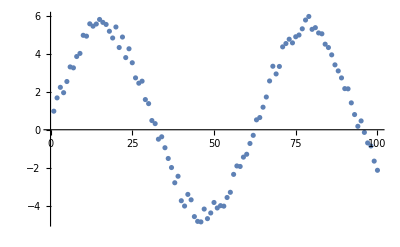

```mathematica
plotNoisySine[100]
```

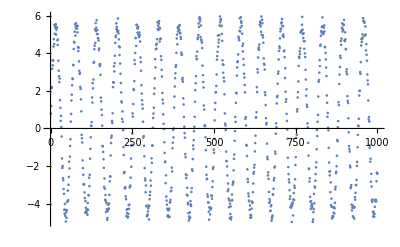

```mathematica
plotNoisySine[1000]
```

注意到 Module 将多个命令汇集在一个函数之中(其实你并不一定需要用 Module来完成它, 但目前来说, 这是一种安全的做法). Module 同时还阻止了数据表达式溢出 - 它是模块的本地表达式. 如果我试着查看它的值:

```mathematica
data
```

data

它并没有具体的数值. Module 有助于保持函数的独立性并且避免了恼人的副作用 (比如当两个不同函数中有相同名称的内部参数时 - 模块会阻止这些干扰). 在帮助页面阅读模块相关内容是非常值得的.

#### 数据的生成与绘制

生成一个 Sin[x] (x∈[0,50]) 步长为 0.1 的数值表. 并画出图表.

Hint: 你将用到 Table 函数, Sin 函数, ListPlot函数, 请在帮助页面查看它们.
Hint 2: 暂时不要担心 x 轴的问题. 如果你不提供任何信息, ListPlot 函数会假设 x 取 {1, 2, 3, ...}. 目前对这些练习来说没问题. 或许你也可以之后重新回到这里来修改 x 轴.

Solution

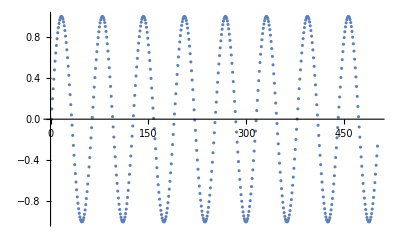

```mathematica
plotTransformedData[fn_,transform_,max_,step_]:=ListPlot[transform[Table[fn[x],{x,0,max,step}]]]

plotTransformedData[Sin,Identity,50,0.1]
```

得益于了解了接下来的练习包含的知识, 我将这里的函数编写得比此练习所需要的更为一般.

#### 函数的不同表达方式

还是上面的练习的问题, 但这次我们生成 Riemann-Siegel 函数 (在 Mathematica 中的函数是 RiemannSiegelZ) 的数值, 做平方运算并画出图标

Hint1: 你只是在做与上题有细微不同的事情, 观察你是否可以重新使用那段代码. 注意重新使用并不意味着复制粘贴. 你可以会需要修改上述代码来确保它对这个问题成立. 需要明确的是, 我是希望你使用上面定义的函数来回答这个问题的一部分 - 如果你认为你需要修改的话. 不要重新定义一个新的绘制函数来解决这个问题 !
Hint 2: 切记, 函数可以作为参数来传递给另外一个函数.
Hint 3: 这一节是关于函数的, 你是否已经定义了一个函数了呢?

Solution

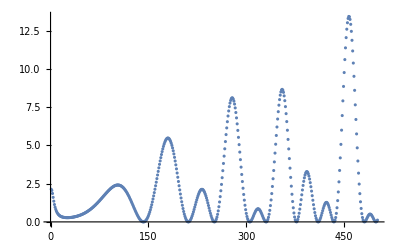

```mathematica
sq[x_]:=x;
plotTransformedData[RiemannSiegelZ,sq,50,0.1]
```

注意到我将始终使用纯函数(pure function)进行平方操作. 我想我不应该跟上这个教程的节奏(再使用函数作为参数的方法)

#### 数据的转换

现在绘制经过傅立叶变换后的 Sin[x] 的模量. 让定义域取为 [0,1000] 步长为 1 

Hint 1: 在帮助页面查询 Abs 函数和 Fourier 函数.
Hint 2: 如果有必要的话, 重新回到第一个问题的解上并使它变得更为一般. 同样的, 我并不需要你定义一个新的函数来解决这个问题 - 修改第一个问题的解法来使其变得足够一般, 并且能够解决这三个问题.
Hint 3: 也许定义一个函数来进行 Fourier 变换和 Abs 运算会有所帮助.
Hint 4: 当你重新修改你的代码时, 你可能会发现 Identity 函数十分有用.
Hint 5: 答案看上可能会很有趣. Mathematica 返回了你预期 Fourier 变换的两倍 - 后半部分与前半部分是镜面对称的.

Solution

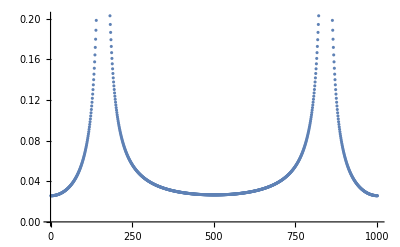

```mathematica
ft[x_]:=Abs[Fourier[x]];
plotTransformedData[Sin,ft,1000,1]
```

我再次用了纯函数

### 纯函数(Pure functions)

好了, 对于命名函数我们讨论得足够了. 是时候来学习新的知识了. 你经常会想写一个 "一次性" 函数, Mathematica 提供了纯函数来满足这个目的 (在其他语言中通常被称为 λ-表达式, 源于邱奇数(Church’s λ-calculus)) [奇怪的是, “纯函数” 在几乎所有其他函数式编程语言中另有所指 - 又是 Wolfram 特立独行的例子]. 用于定义纯函数的函数被直接称为 Function 。举个例子:

```mathematica
Function[2#^2]
```

2 #1^2&

# 符号用于表示函数的参数 (如果你使用的参数多于一个, 你可以使用 #1, #2 等). 这样就定义了一个函数(我们刚才在上面定义这种函数现在基本没用, 因为它没有函数名, 所以我们无法引用它 (除非在必要时使用 %)). 这类函数的调用方式与其他任何函数相同 - 通过在方括号内加上参数:

```mathematica
Function[2 #^2][4]
```

32

这看起来似乎十分笨拙, 因为我们每次都必须重新编写这类函数, 但记住这类纯函数意味着用完就扔. 如果你发现你在重新编写同样的纯函数, 那么或许你应该定义一个命名函数. 编写纯函数在 Mathematica 也是一件十分常见的事情, 所以也有一个更加简洁的表达式 (事实上, 你可以在 Mathematica 的输出上看见它) : 在函数体后加上后缀 &

```mathematica
2#^2&[4]
```

32

其中, 2#^2& 是一个匿名纯函数, 我调用它并代入参数 4, 得到 2 4^2=32.

在列表上映射一个纯函数是一种非常常见用法. 比如, 如果我想把列表中每个元素都进行 3x+5 运算:

```mathematica
l={1,2,99,1000};
(3#+5)&/@l
```

{8,11,302,3005}

[Note: 代码中的小括号并不是必要的, 但我认为它们会帮助你更好的理解.]
[Advanced note: 由于组成函数的简单代数运算被标记为可列(Listable), 这意味着它会自动映射到列表上, 因此我在这里根本不需要 Map 函数. 暂时先忽略这个, 但把它记在脑海中, 因为在某天它可能会让你出差错 ]

对数据集进行操控是在列表上映射一个纯函数的常见用法. 试想我有一个形如 {{x_1,y_1},{x_2,y_2},...} 的列表, 我想对x 数据进行规范化(normalize)并偏移(offset) , 同时对 y 数据进行对数运算. 一个常规的做法就是编写一个转化 {x,y} 数据对的纯函数, 接着把它映射到列表上:

```mathematica
dat={{0,1},{1,3},{2,9},{3,16},{4,25}};
{(#⟦1⟧-2)/2,Log[#⟦2⟧]}&/@dat
```

{{-1,0},{-1/2,Log[3]},{0,Log[9]},{1/2,Log[16]},{1,Log[25]}}

弄清楚在这里发生了什么: 纯函数(在 & 前的代码) 只代入一个简单的参数(只有 #, 没有 #1, #2, 等等) 这个参数至少必须是一个有两个元素的列表, 因为我需要代入列表中的那两个元素. (其中 #⟦1⟧ 表示列表中的第一个元素 (x值), #⟦2⟧ 表示第二个元素 (y值). ( 你可以通过键入 esc [ [ 来达到这个效果 - 这个一个快捷方式, 你可以在帮助页面找到. ) ) 纯函数返回了一个带有两个元素(花括号内)的列表.  接着我将这个纯函数映射到整个数据集上.

这可能会一点难以理解, 我们来通过几个例子来熟悉这些想法.

#### 一个简单的纯函数

编写一个进行以 5 为底的指数运算的纯函数, 并计算 5^99

Solution

```mathematica
5^#&[99]
```

1577721810442023610823457130565572459346412870218046009540557861328125

#### 列表的计算

编写一个运算双元素列表的纯函数. 其中, 对第一个元素进行以 5 为底的指数运算, 对第二个元素进行 5 次方幂运算. 并代入参数 5. [答案应该为 {3125,3125}].

Solution

```mathematica
{5^#,#^5}&[5]
```

{3125,3125}

#### 列表的映射

```mathematica
l={1,8,75,300};
```

编写一个计算  log(x)+sin(x) 的纯函数. 并对列表 l 的每一个元素都进行运算.

Solution

```mathematica
Log[#]+Sin[#]&/@l
```

{Sin[1],Log[2]+Sin[2],Log[99]+Sin[99],Log[1000]+Sin[1000]}

#### 生成列表中的列表

```mathematica
l={1,2,4,8};
```

编写一个对于参数 x 生成列表 {x,x^2} 的纯函数. 将它映射到列表 l 上. [你的答案应该是 {{1,1},{2,4},{4,16},{8,64}} ].

Solution

```mathematica
{#,#^2}&/@l
```

{{1,1},{2,4},{99,9801},{1000,1000000}}

#### 嵌套列表的操作

```mathematica
l={{1,5},{7,89},{43,60}};
```

编写一个参数为双元素列表 {x,y} 并计算出 {x+y,x-y} 的纯函数. 将它映射到列表 l 上. [你应该得到  {{6,-4},{96,-82},{103,-17}} ].

Solution

```mathematica
{#⟦1⟧+#⟦2⟧,#⟦1⟧-#⟦2⟧}&/@l
```

{{6,-4},{96,-82},{103,-17}}

### Apply 函数

你已经掌握了关于纯函数的知识, 现在我们将进入本教程这一部分最后一个概念的学习, Apply 函数. 由于Apply 函数从底层操控 Mathematica 的表达式结构, 因此它起初会十分难以理解. 但实际上它十分有用, 搞清楚它到底是如何工作的大有脾益. 让我先来深入看 Mathematica 表达元素的方式. FullForm 命令将让我们深入了解表达式结构; 它向我们展示了内核对表达式的表示方法:

```mathematica
a+b//FullForm
```

Plus[a,b]

```mathematica
a b//FullForm
```

Times[a,b]

```mathematica
{a,b}//FullForm
```

List[a,b]

```mathematica
a^x+b^y+5x//FullForm
```

Plus[Power[a,x],Power[b,y],Times[5,x]]

你看到了 Mathematica 的表达式是以 “头部” 形式表达的[表达式序列或者原子序列], 头部是一个像 List, Plus, Power的符号, 或者像 x, a, b, 5 的原子. 这就是我在之前说过的统一的表达式. 一切对象都可以被表示为这些嵌套列表表达式之一是一件十分简单但又强大的思想. 查看各种 Mathematica 表达式的 FullForms（和 TreeForms）是非常有启发性的. 你可以思考下面这个例子:

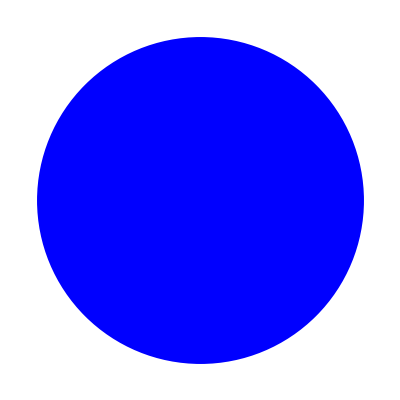
```mathematica
{FullForm[#],TreeForm[#]}&[-Graphics-]
```

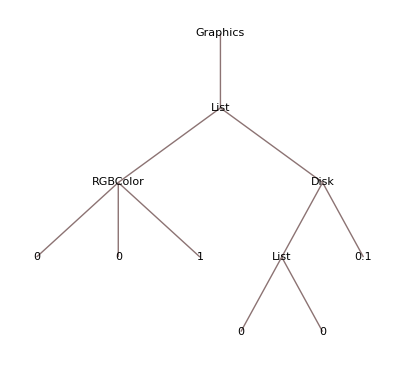
{Graphics[List[RGBColor[0,0,1],Disk[List[0,0],0.1]]],-Graphics-}

但是我们现在不应该被所有这些优雅的东西分心. 回到 Apply 函数. 注意到表达式 {a,b} 和 a+b 的差别只在于它们的头部. Apply 函数可以让我修改表达式的头部 - 有效地将其改变为另一种对象. 我们可以将一个列表变为求和, 如下:

```mathematica
Apply[Plus,{a,b}]
```

a+b

同样地, Apply 函数也有简洁的中缀表示法- @@ :

```mathematica
Plus@@{a,b}
```

a+b

下面有更多复杂的例子, 通过将 Apply 函数映射到列表的方法来进行幂运算 (我编写了一个纯函数来进行操作(!))

```mathematica
l={{a,3},{b,6},{d,11}};
Power@@#&/@l
```

{a^3,b^6,d^11}

映射 Apply 函数同样经常使用, 所以也有简洁记号- @@@:

```mathematica
Power@@@l
```

{a^3,b^6,d^11}

我们可以用如下方式生成一个多项式:

```mathematica
Plus@@Power@@@l
```

a^3+b^6+d^11

你会开始感受到这种统一的表达式如何使编写代码变得容易. 下面来看一些练习.

#### Simple Apply

```mathematica
s=a+b+c+d;
```

将上面的求和形式改为列表. [你的答案应该是 {a,b,c,d} ].

Solution

```mathematica
List@@s
```

{a,b,c,d}

#### Mapped Apply

```mathematica
p=(a+b)(c+d)(e+f);
```

将 p 中的变量提取为嵌套列表. [你的答案应该是 {{a,b},{c,d},{e,f}} ].
Hint: 你可以使用 FullForm 来查看整个输出前后表达式是怎么样的

Solution

```mathematica
List@@@List@@p
```

{{a,b},{c,d},{e,f}}

## A worked example

下面是一个将我们刚刚介绍的概念组合在一起的示例. 这个例子展示了一旦你习惯于处理函数和列表, 你可以在 Mathematica 中简洁地做十分复杂的工作.

### Power series expansions of an exponential

我想要绘制出函数 Sin[x] 的一部分的不同阶数的级数展开式, 并将其与函数本身作比较. 我会将所有图像以不同颜色绘制在同一张图上.

下面是代码. 我们会稍后拆分它. 你可以在滑动条上改变展开式的最高阶数.

Note: 有许多 Mathematica 内置函数可以替换这个例子中我直接编写的代码. 一般情况下，如果函数存在，你应该使用它，但这里为了演示，我不使用.

```mathematica
Manipulate[
Show[MapThread[
Plot[Tooltip[#1,#1],{x,0,4π},PlotStyle->#2,PlotRange->{All,{-3,3}}]&,{
Join[{Sin[x]},Plus@@Table[(-1)^(n+1)/((2 n-1)!)x^(2n-1),{n,1,#}]&/@Range[highestOrder]],
Hue[1-(#-1)/(highestOrder+1)]&/@Range[highestOrder+1]
}]],
{highestOrder,0,16,1}]
```

#### Step-by-step

下面是我如何一步步构建这个函数的. 这也跟我编写它的顺序一致.

首先我想要生成级数展开式. 前十项是:

```mathematica
Table[(-1)^(n+1)/((2 n-1)!)x^(2n-1),{n,1,10}]
```

我可以通过将 List 头部转化为 Plus 头部的方式来对它进行求和 (Sum 函数可以直接一步到位, 但这种方式更加有趣 ! (或者你也可以搭配使用 Series 函数和 Normal 函数)).

```mathematica
Plus@@Table[(-1)^(n+1)/((2 n-1)!)x^(2n-1),{n,1,10}]
```

现在我们将这个最高阶数表示式转化为一个纯函数.

```mathematica
Plus@@Table[(-1)^(n+1)/((2 n-1)!)x^(2n-1),{n,1,#}]&[10]
```

通过将该纯函数映射到 Range 来生成阶数由 1 到 10 的展开式列表.

```mathematica
Plus@@Table[(-1)^(n+1)/((2 n-1)!)x^(2n-1),{n,1,#}]&/@Range[10]
```

用 Join 函数将原函数附加到这个展开式列表的开头.

```mathematica
Join[{Sin[x]},Plus@@Table[(-1)^(n+1)/((2 n-1)!)x^(2n-1),{n,1,#}]&/@Range[10]]
```

编写一个二元纯函数 - 绘制函数和绘制颜色. 我会使用Tooltip函数和 Plot 函数, 这样的话, 如果您将鼠标悬停在上方你会看到不同绘制结果的函数.

```mathematica
Plot[Tooltip[#1,#1],{x,0,10},PlotStyle->#2]&
```

Plot[#1,{x,0,10},PlotStyle→#2]&

现在我们想要用不同的颜色列来表示不同的函数列. MapThread 作为更一般的 Map 函数可以达到这个目的.

```mathematica
highestOrder=10;
MapThread[
Plot[Tooltip[#1,#1],{x,0,10},PlotStyle->#2,PlotRange->{All,{0,1000}}]&,
{
Join[{Sin[x]},Plus@@Table[(-1)^(n+1)/((2 n-1)!)x^(2n-1),{n,1,#}]&/@Range[10]],Hue[1-(#-1)/(highestOrder+1)]&/@Range[highestOrder+1]
}];
```

我们已经生成了一组图像表达式列表, 现在我们只需要将它们一起显示出来即可. Show 函数可以达到这样的目的.

```mathematica
Show[
MapThread[
Plot[Tooltip[#1,#1],{x,0,10},PlotStyle->#2,PlotRange->{All,{-3,3}}]&,{
Join[{Sin[x]},Plus@@Table[(-1)^(n+1)/((2 n-1)!)x^(2n-1),{n,1,#}]&/@Range[10]],Hue[1-(#-1)/(highestOrder+1)]&/@Range[10+1]
}
]
]
```

剩下的就是使用 Manipulate 函数来达到在滑动条上改变展开式的最高阶数的目的.

## Playtime

下面有一些自由练习供你来练习上面所介绍的技术. 试着用 Mathematica 风格的方法来解决它们. 如果你不能将它们全部解决, 不用担心, 它们对你理解后续的内容不影响.

#### Expression building

编写一个二元函数, 其中一个参数为一列数{c_0,c_1,c_2,…}, 另一个是 x . 并计算给定 x 后 c_0+c_1 x+c_2 x^2+… 的值.

Solution

```mathematica
evalPoly[c_,x_]:=Plus@@(c(x^#&/@Range[0,Length[c]-1]))
evalPoly[{1,7,6,5,4},3]
```

解决这个问题有十分多的解法. 我的解法是将 x 转化为与{c_0,c_1,c_2,…} 相同长度的列表, 并加上对应的方幂. 接着将这两个列表相乘 (Mathematica 默认将两个列表对应的数相乘). 最后将 List 头部转化为 Plus 头部.

#### Radical!

编写一个函数来计算 √(6+√(6+√(6+…)))的值, 其中可以有任意个 “6” . 生成一个从 1 个 “6” 到 10 个 “6” 的列表.
Hint 1: 你可能想重新复习一下另一个高阶函数, Nest 函数.
Hint 2: Mathematica 会尽可能地追踪一切对象. 你可能需要函数 N 来将你的答案转化为数值解.

Solution

```mathematica
radical[n_]:=Nest[√(6+#)&,0,n]
radical/@Range[10]//N
```

{2.44949,2.9068,2.98443,2.9974,2.99957,2.99993,2.99999,3.,3.,3.}

#### π

使用 Leibniz 公式计算 π, π=4∑_(j=0)^∞ (-1)^j/(2 j+1). 
编写一个以整数 n 为参数的函数, 并计算级数前 n 项和. 绘制 n 从 1 到 20 产生的值. 并在同一张图上绘制 π 的精确值.
Hint: Mathematica 有内置 Sum 函数
Note: Mathematica 可以进行无穷求和解析运算 - 尝试一下 !

Solution

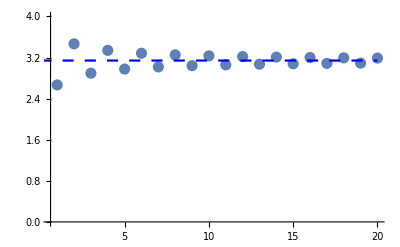

```mathematica
Show[
ListPlot[4∑_(j=0)^# (-1)^j/(2 j+1)&/@Range[20],PlotStyle->PointSize[0.02],PlotRange->{All,{0,4}}],
Plot[π,{x,0,20},PlotStyle->{Blue,Dashing[{0.02,0.02}]}]
]
```

```mathematica
4∑_(j=0)^∞ (-1)^j/(2 j+1)
```

π

#### Monte Carlo π

你可以通过以下方式来近似 π ,首先生成在单位正方形上均匀分布的点阵, 然后计算它们中的哪一部分位于单位圆圈内. 编写一个生成 n 个点的函数.
Advanced: 你可以绘制点阵和圆吗? 你可以将位于圆内的点标为红色, 在圆外的点标为蓝色吗?

Solution

一个使用模式匹配器的漂亮但难懂的单行指令.

```mathematica
4./# Count[Norm/@Table[{Random[],Random[]},{#}],l_/;l<1]&[10^6]
```

3.14176

其他可行解

```mathematica
points[n_]:=Partition[RandomReal[{-1,1},n],{2}]
mcPi[n_]:=8 Length[Select[Plus@@@(points[n]^2),#<1&]]/n
mcPi[10^6]//N
```

3.14243

绘制

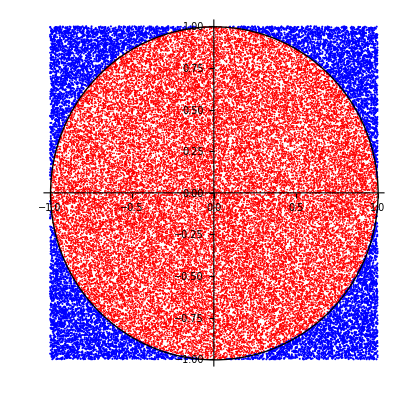
{-Graphics-,3.14032}

```mathematica
plotMCPi[n_]:=Module[{p,pSq,inCircle},
p=points[n];
pSq=Plus@@@(p^2);
inCircle=#<1&/@pSq;
{Show[
ListPlot[Pick[p,inCircle],PlotStyle->Red],
ListPlot[Pick[p,Not/@inCircle],PlotStyle->Blue],
Graphics[Circle[{0,0},1]],
AspectRatio->1
],
4 Count[inCircle,True]/Length[p]//N
}
]
plotMCPi[10^5]
```